```mathematica
Integrate[y^4 ⅇ^(-y^2), {y, -10, x}]
```

1/8 (-4060/ⅇ^100-2 ⅇ^(-x^2) x (3+2 x^2)+3 √π Erf[10]+3 √π Erf[x])

```mathematica
(*f[x_]:=x^4 ⅇ^(-x^2)*)
f[x_]:=1/8 (-4060/ⅇ^100-2 ⅇ^(-x^2) x (3+2 x^2)+3 √π Erf[10]+3 √π Erf[x])
```

```mathematica
a=Plot[f[x], {x, -10, 10}, PlotRange->All];
```

```mathematica
chebinterp=Import["testfile.txt", "Data"];
```

```mathematica
b=ListPlot[chebinterp];
```

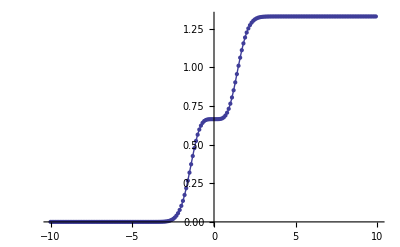

```mathematica
Show[a,b]
```

```mathematica
abserror=Table[{chebinterp⟦i,1⟧, chebinterp⟦i,2⟧-f[chebinterp⟦i,1⟧]}, {i, Length[chebinterp]}];
```

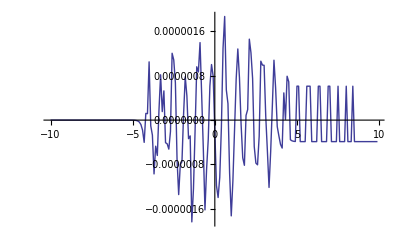

```mathematica
ListLinePlot[abserror]
```

```mathematica
avgerror=Table[{chebinterp⟦i,1⟧, 2*(chebinterp⟦i,2⟧-f[chebinterp⟦i,1⟧])/(chebinterp⟦i,2⟧+f[chebinterp⟦i,1⟧])}, {i, Length[chebinterp]}];
```

Power::infy: Infinite expression 1/0. encountered.

∞::indet: Indeterminate expression 0.\ ComplexInfinity encountered.

Power::infy: Infinite expression 1/0. encountered.

∞::indet: Indeterminate expression 0.\ ComplexInfinity encountered.

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power :: "infy" will be suppressed during this calculation.

∞::indet: Indeterminate expression 0.\ ComplexInfinity encountered.

General::stop: Further output of ∞ :: "indet" will be suppressed during this calculation.

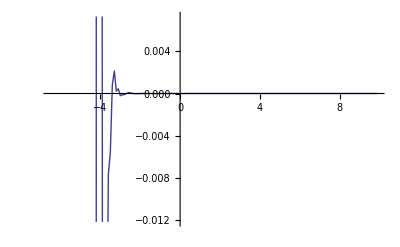

```mathematica
ListLinePlot[avgerror]
```

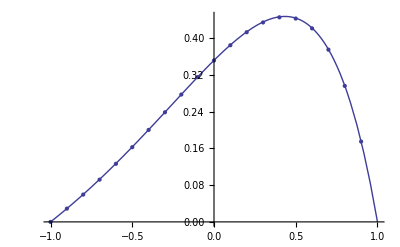

```mathematica
f[x_]:=ⅇ^x-Sinh[1]/Sinh[2] ⅇ^(2 x)-ⅇ/(1+ⅇ^2)
chebinterp=Import["testfile2.txt", "Data"];
a=Plot[f[x], {x, -1, 1}, PlotRange->All];
b=ListPlot[chebinterp];
Show[a,b]
```

```mathematica
L={{4, -4,  4, -12,  32}, {0,  4, -16,  24, -32}, {0,  0,  4, -24,  48}, {1, -1,  1, -1,  1}, {1,  1,  1,  1,  1}}
```

{{4,-4,4,-12,32},{0,4,-16,24,-32},{0,0,4,-24,48},{1,-1,1,-1,1},{1,1,1,1,1}}

```mathematica
s={-0.060085, 1.130318, 0.271495, 0.000000, 0.000000}
```

{-0.060085,1.13032,0.271495,0.,0.}

```mathematica
u=LinearSolve[L, s]
```

{0.149997,0.0845164,-0.123704,-0.0845164,-0.0262934}

```mathematica
L.u-s
```

{5.55112×10^-17,-4.44089×10^-16,-1.11022×10^-16,3.1225×10^-17,-1.35308×10^-16}

```mathematica
s[x_]:=ⅇ^x-(4 ⅇ)/(1+ⅇ^2)
```

```mathematica
n=4;
j=3;
xi=Table[Cos[(π i)/T], {i, 0, T, 1}];
sum=0;
For[i=0, i≤n, i++,
a=s[xi⟦i⟧]ChebyshevT[j, xi⟦i⟧];
a=2/n(Sum[s[xi⟦i⟧]ChebyshevT[j, xi⟦i⟧], {i, 2, n}]+1/2(s[xi⟦1⟧]ChebyshevT[j, xi⟦1⟧]+s[xi⟦n+1⟧]ChebyshevT[j, xi⟦n+1⟧]));
N[a]
```

0.0448798

```mathematica
n=4;
j=3;
```

```mathematica
If[j==0||n, 1/2, 1]
```

If[4,1/2,1]

```mathematica
n=4;
j=3;
sum=0;
For[i=0, i≤n, i++,
a=s[Cos[(π i)/n]]ChebyshevT[j, Cos[(π i)/n]];
b=If[i==0||n, a/2, a] ;
sum+=b;
]
N[2/n*If[j==0||n, 1/2, 1] *sum]
```

0.5 If[4.,1. 0.5,1.] (0.711087+4. If[4.,a 0.5,a])

```mathematica
x={0.000000, 0.156434, 0.309017, 0.453990, 0.587785, 0.707107, 0.809017, 0.891007, 0.951057, 0.987688, 1.000000};
y={1,  0.960229,  0.850161,  0.693826,  0.521077,  0.358188,  0.222157,  0.11995,  0.0512597,  0.012462,  3.89804*^-17};
```

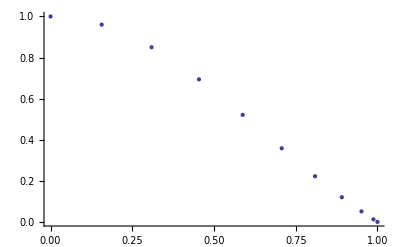

```mathematica
ListPlot[Table[{x⟦i⟧, y⟦i⟧}, {i, Length[x]}]]
```

```mathematica
T={{1, -1, 1, -1, 1}, {1, -1/√2, 0, 1/√2, -1}, {1, 0, -1, 0, 1}, {1, 1/√2, 0, -1/√2, -1}, {1, 1, 1, 1, 1}}
L={{0, 8, 0, 24, 0}, {0, 0, 32, 0, 0}, {0, 0, 0, 48, 0}, {0, 0, 0, 0, 0}, {0, 0, 0, 0, 0}}
s={1,  0.775927,  0.358188,  0.0816092,  3.89804*^-17}
```

{{1,-1,1,-1,1},{1,-1/(√2),0,1/(√2),-1},{1,0,-1,0,1},{1,1/(√2),0,-1/(√2),-1},{1,1,1,1,1}}

{{0,8,0,24,0},{0,0,32,0,0},{0,0,0,48,0},{0,0,0,0,0},{0,0,0,0,0}}

{1,0.775927,0.358188,0.0816092,3.89804×10^-17}

```mathematica
T.L
```

{{0,8,-32,72,0},{0,8,-16 √2,24,0},{0,8,0,-24,0},{0,8,16 √2,24,0},{0,8,32,72,0}}

```mathematica
u=LinearSolve[T.L, s]
```

LinearSolve::nosol: Linear equation encountered that has no solution.

LinearSolve[{{0,8,-32,72,0},{0,8,-16 √2,24,0},{0,8,0,-24,0},{0,8,16 √2,24,0},{0,8,32,72,0}},{1,0.775927,0.358188,0.0816092,3.89804×10^-17}]

```mathematica
T={{1, -1, 1, -1, 1}, {1, -1/√2, 0, 1/√2, -1}, {1, 0, -1, 0, 1}, {1, 1/√2, 0, -1/√2, -1}, {1, 1, 1, 1, 1}}
L={{0, 8, 0, 24, 0}, {0, 0, 32, 0, 0}, {0, 0, 0, 48, 0}, {0, 0, 0, 0, 0}, {0, 0, 0, 0, 0}}
s={1,  0.775927,  0.358188,  0.0816092,  3.89804*^-17}
```

```mathematica
TL={{8,-16 √2,24,0},{8,0,-24,0},{8,16 √2,24,0},{8,32,72,0}}
```

{{8,-16 √2,24,0},{8,0,-24,0},{8,16 √2,24,0},{8,32,72,0}}

```mathematica
s={0.775927,  0.358188,  0.0816092,  3.89804*^-17}
```

{0.775927,0.358188,0.0816092,3.89804×10^-17}

```mathematica
u=LinearSolve[TL, s]
```

LinearSolve::nosol: Linear equation encountered that has no solution.

LinearSolve[{{8,-16 √2,24,0},{8,0,-24,0},{8,16 √2,24,0},{8,32,72,0}},{0.775927,0.358188,0.0816092,3.89804×10^-17}]

```mathematica
f[x_]:=ϕ0*ChebyshevT[0, x]+ϕ1*ChebyshevT[2, x]+ϕ2*ChebyshevT[4, x]
```

```mathematica
Expand[Simplify[f''[x]+2/x f'[x]]]
```

12 ϕ1-48 ϕ2+160 x^2 ϕ2

```mathematica
Expand[Simplify[1/x f'[x]]]
```

4 ϕ1-16 ϕ2+32 x^2 ϕ2

```mathematica
Expand[Simplify[f''[x]]]
```

4 ϕ1-16 ϕ2+96 x^2 ϕ2

```mathematica
inv={{0, 1, 0, -1, 0, 1}, {0, 0, 2, 0, -2, 0}, {0, 0, 0, 2, 0, -2}, {0, 0, 0, 0, 2, 0}, {0, 0, 0, 0, 0, 2}, {0, 0, 0, 0, 0, 0}}
```

{{0,1,0,-1,0,1},{0,0,2,0,-2,0},{0,0,0,2,0,-2},{0,0,0,0,2,0},{0,0,0,0,0,2},{0,0,0,0,0,0}}

```mathematica
D1={{0, 1, 0, 3, 0, 5}, {0, 0, 4, 0, 8, 0}, {0, 0, 0, 6, 0, 10}, {0, 0, 0, 0, 8, 0}, {0, 0, 0, 0, 0, 10}, {0, 0, 0, 0, 0, 0}}
```

{{0,1,0,3,0,5},{0,0,4,0,8,0},{0,0,0,6,0,10},{0,0,0,0,8,0},{0,0,0,0,0,10},{0,0,0,0,0,0}}

```mathematica
inv.D1//MatrixForm
```

(0 | 0 | 4 | 0 | 0 | 0
0 | 0 | 0 | 12 | 0 | 0
0 | 0 | 0 | 0 | 16 | 0
0 | 0 | 0 | 0 | 0 | 20
0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0)

```mathematica
f[x_]:=ϕ0*ChebyshevT[0, x]+ϕ1*ChebyshevT[1, x]+ϕ2*ChebyshevT[2, x]+ϕ3*ChebyshevT[3, x]
```

```mathematica
f[x]
```

ϕ0+x ϕ1+(-1+2 x^2) ϕ2+(-3 x+4 x^3) ϕ3

```mathematica
Expand[f[x]/x]
```

ϕ0/x+ϕ1-ϕ2/x+2 x ϕ2-3 ϕ3+4 x^2 ϕ3

```mathematica
Expand[(ϕ0-ϕ2)/x+ϕ1*ChebyshevT[0, x]+2*ϕ2*ChebyshevT[1, x]+2*ϕ3*ChebyshevT[2, x]-ϕ3*ChebyshevT[0, x]]
```

ϕ0/x+ϕ1-ϕ2/x+2 x ϕ2-3 ϕ3+4 x^2 ϕ3

{{0.,0.},{0.01,-1.50291×10^-12},{0.02,-6.75405×10^-12},{0.03,-1.51216×10^-11},{0.04,-2.66964×10^-11},{0.05,-4.13421×10^-11},{0.06,-5.88863×10^-11},{0.07,-7.91216×10^-11},{0.08,-1.01812×10^-10},{0.09,-1.26694×10^-10},{0.1,-1.53478×10^-10},{0.11,-1.81858×10^-10},{0.12,-2.1151×10^-10},{0.13,-2.42101×10^-10},{0.14,-2.73291×10^-10},{0.15,-3.04736×10^-10},{0.16,-3.36099×10^-10},{0.17,-3.67046×10^-10},{0.18,-3.97258×10^-10},{0.19,-4.26432×10^-10},{0.2,-4.54284×10^-10},{0.21,-4.80554×10^-10},{0.22,-5.05011×10^-10},{0.23,-5.27453×10^-10},{0.24,-5.47709×10^-10},{0.25,-5.65646×10^-10},{0.26,-5.81164×10^-10},{0.27,-5.94201×10^-10},{0.28,-6.04731×10^-10},{0.29,-6.12767×10^-10},{0.3,-6.18354×10^-10},{0.31,-6.21575×10^-10},{0.32,-6.22544×10^-10},{0.33,-6.21404×10^-10},{0.34,-6.18325×10^-10},{0.35,-6.13503×10^-10},{0.36,-6.07151×10^-10},{0.37,-5.99498×10^-10},{0.38,-5.90787×10^-10},{0.39,-5.81264×10^-10},{0.4,-5.7118×10^-10},{0.41,-5.60786×10^-10},{0.42,-5.50322×10^-10},{0.43,-5.4002×10^-10},{0.44,-5.30098×10^-10},{0.45,-5.20752×10^-10},{0.46,-5.12161×10^-10},{0.47,-5.04475×10^-10},{0.48,-4.9782×10^-10},{0.49,-4.9229×10^-10},{0.5,-4.87952×10^-10},{0.51,-4.8484×10^-10},{0.52,-4.82958×10^-10},{0.53,-4.82282×10^-10},{0.54,-4.82756×10^-10},{0.55,-4.84301×10^-10},{0.56,-4.86812×10^-10},{0.57,-4.90164×10^-10},{0.58,-4.94216×10^-10},{0.59,-4.98814×10^-10},{0.6,-5.03794×10^-10},{0.61,-5.08989×10^-10},{0.62,-5.14235×10^-10},{0.63,-5.19369×10^-10},{0.64,-5.24242×10^-10},{0.65,-5.28717×10^-10},{0.66,-5.32676×10^-10},{0.67,-5.36024×10^-10},{0.68,-5.38686×10^-10},{0.69,-5.40618×10^-10},{0.7,-5.418×10^-10},{0.71,-5.4224×10^-10},{0.72,-5.41974×10^-10},{0.73,-5.41062×10^-10},{0.74,-5.39587×10^-10},{0.75,-5.37653×10^-10},{0.76,-5.35375×10^-10},{0.77,-5.32879×10^-10},{0.78,-5.30298×10^-10},{0.79,-5.27758×10^-10},{0.8,-5.25381×10^-10},{0.81,-5.23274×10^-10},{0.82,-5.21524×10^-10},{0.83,-5.20195×10^-10},{0.839999,-5.19323×10^-10},{0.849999,-5.18913×10^-10},{0.859999,-5.18943×10^-10},{0.869999,-5.19357×10^-10},{0.879999,-5.20079×10^-10},{0.889999,-5.2101×10^-10},{0.899999,-5.2204×10^-10},{0.909999,-5.23059×10^-10},{0.919999,-5.23964×10^-10},{0.929999,-5.24673×10^-10},{0.939999,-5.25137×10^-10},{0.949999,-5.25346×10^-10},{0.959999,-5.25334×10^-10},{0.969999,-5.25174×10^-10},{0.979999,-5.24967×10^-10},{0.989999,-5.24807×10^-10},{0.999999,-5.24729×10^-10},{-1.,0.},{-0.99,0.},{-0.98,0.},{-0.97,0.},{-0.96,0.},{-0.95,0.},{-0.94,0.},{-0.93,0.},{-0.92,0.},{-0.91,0.},{-0.9,0.},{-0.89,0.},{-0.88,0.},{-0.87,0.},{-0.86,0.},{-0.85,0.},{-0.84,0.},{-0.83,0.},{-0.82,0.},{-0.81,0.},{-0.8,0.},{-0.79,0.},{-0.78,0.},{-0.77,0.},{-0.76,0.},{-0.75,0.},{-0.74,0.},{-0.73,0.},{-0.72,0.},{-0.71,0.},{-0.7,0.},{-0.69,0.},{-0.68,0.},{-0.67,0.},{-0.66,0.},{-0.65,0.},{-0.64,0.},{-0.63,0.},{-0.62,0.},{-0.61,0.},{-0.6,0.},{-0.59,0.},{-0.58,0.},{-0.57,0.},{-0.56,0.},{-0.55,0.},{-0.54,0.},{-0.53,0.},{-0.52,0.},{-0.51,0.},{-0.5,0.},{-0.49,0.},{-0.48,0.},{-0.470001,0.},{-0.460001,0.},{-0.450001,0.},{-0.440001,0.},{-0.430001,0.},{-0.420001,0.},{-0.410001,0.},{-0.400001,0.},{-0.390001,0.},{-0.380001,0.},{-0.370001,0.},{-0.360001,0.},{-0.350001,0.},{-0.340001,0.},{-0.330001,0.},{-0.320001,0.},{-0.310001,0.},{-0.300001,0.},{-0.290001,0.},{-0.280001,0.},{-0.270001,0.},{-0.260001,0.},{-0.250001,0.},{-0.240001,0.},{-0.230001,0.},{-0.220001,0.},{-0.210001,0.},{-0.200001,0.},{-0.190001,0.},{-0.180001,0.},{-0.170001,0.},{-0.160001,0.},{-0.150001,0.},{-0.140001,0.},{-0.130001,0.},{-0.120001,0.},{-0.110001,0.},{-0.100001,0.},{-0.090001,0.},{-0.080001,0.},{-0.070001,0.},{-0.060001,0.},{-0.050001,0.},{-0.040001,0.},{-0.030001,0.},{-0.020001,0.},{-0.010001,0.},{-1.×10^-6,0.},{0.009999,0.},{0.019999,0.},{0.029999,0.},{0.039999,0.},{0.049999,0.},{0.059999,0.},{0.069999,0.},{0.079999,0.},{0.089999,0.},{0.099999,0.},{0.109999,0.},{0.119999,0.},{0.129999,0.},{0.139999,0.},{0.149999,0.},{0.159999,0.},{0.169999,0.},{0.179999,0.},{0.189999,0.},{0.199999,0.},{0.209999,0.},{0.219999,0.},{0.229999,0.},{0.239999,0.},{0.249999,0.},{0.259999,0.},{0.269999,0.},{0.279999,0.},{0.289999,0.},{0.299999,0.},{0.309999,0.},{0.319999,0.},{0.329999,0.},{0.339999,0.},{0.349999,0.},{0.359999,0.},{0.369999,0.},{0.379999,0.},{0.389999,0.},{0.399999,0.},{0.409999,0.},{0.419999,0.},{0.429999,0.},{0.439999,0.},{0.449999,0.},{0.459999,0.},{0.469999,0.},{0.479999,0.},{0.489999,0.},{0.499999,0.},{0.509999,0.},{0.519999,0.},{0.529999,0.},{0.539999,0.},{0.549999,0.},{0.559999,0.},{0.569999,0.},{0.579999,0.},{0.589999,0.},{0.599999,0.},{0.609999,0.},{0.619999,0.},{0.629999,0.},{0.639999,0.},{0.649999,0.},{0.659999,0.},{0.669999,0.},{0.679999,0.},{0.689999,0.},{0.699999,0.},{0.709999,0.},{0.719999,0.},{0.729999,0.},{0.739999,0.},{0.749999,0.},{0.759999,0.},{0.769999,0.},{0.779999,0.},{0.789999,0.},{0.799999,0.},{0.809999,0.},{0.819999,0.},{0.829999,0.},{0.839999,0.},{0.849999,0.},{0.859999,0.},{0.869999,0.},{0.879999,0.},{0.889999,0.},{0.899999,0.},{0.909999,0.},{0.919999,0.},{0.929999,0.},{0.939999,0.},{0.949999,0.},{0.959999,0.},{0.969999,0.},{0.979999,0.},{0.989999,0.},{0.999999,0.}}

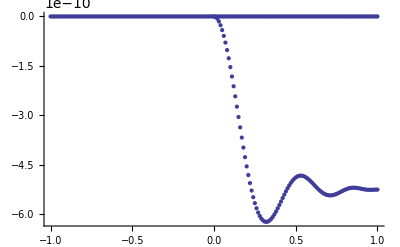

```mathematica
phidata=Import["phigamma2.txt", "Data"]
ListPlot[phidata]
```

```mathematica
phi[x_]:=-1-Sin[π*x]/(π*x)
```

```mathematica
phiout[x_]:=(x-1)/2
```

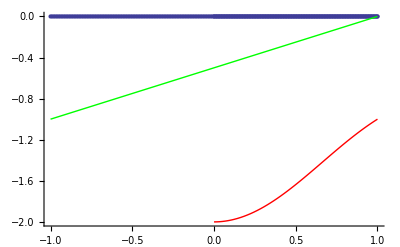

```mathematica
phianalytic=Plot[phi[x], {x, 0, 1}, PlotStyle->Red];
phioutanalytic=Plot[phiout[x], {x, -1, 1}, PlotStyle->Green];
phinumeric=ListPlot[phidata];
Show[phinumeric, phianalytic, phioutanalytic]
```

```mathematica
Expand[(x-1)^4]
```

1-4 x+6 x^2-4 x^3+x^4

```mathematica
Expand[35/8 ChebyshevT[0, x]-7ChebyshevT[1, x]+7/2 ChebyshevT[2, x]-ChebyshevT[3, x]+1/8 ChebyshevT[4, x]]
```

1-4 x+6 x^2-4 x^3+x^4

```mathematica
R=5;
fin[r_]:=(R*r^2)/6-r^4/(20R)-(3 R^3)/4
fout[r_]:=R^5/(2 r^2)-(17 R^4)/(15r)
```

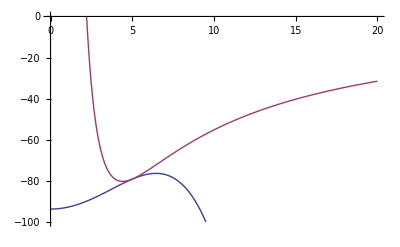

```mathematica
plot1=Plot[{fin[r], fout[r]}, {r, 0, 20}, PlotRange->{-100, 0}]
```

```mathematica
N[fin[0]]
```

-93.75

```mathematica
fout[1.1]
```

-0.61708

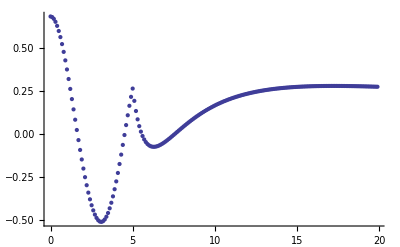

```mathematica
phidata=Import["phigamma2.txt", "Data"];
plot2=ListPlot[phidata]
```

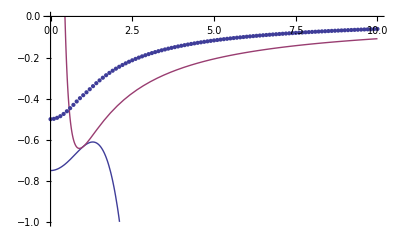

```mathematica
Show[plot1, plot2]
```

```mathematica
f0[r_]:=-67/240+7/120(2 r^2-1)-1/160(8 r^4-8 r^2+1)
```

```mathematica
f0'[1]
```

2/15

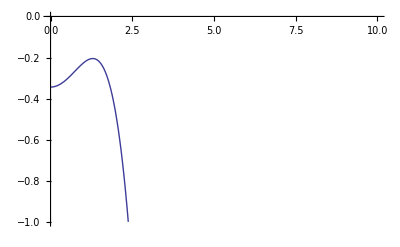

```mathematica
plot3=Plot[-67/240+7/120(2 r^2-1)-1/160(8 r^4-8 r^2+1)(*-0.407*), {r, 0, 10}, PlotRange->{-1, 0}]
```

```mathematica
x[r_]:=1-2/r
```

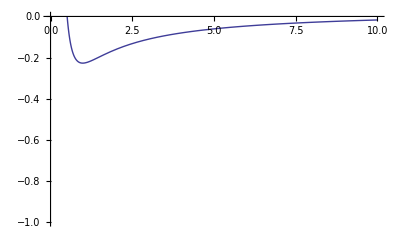

```mathematica
plot4=Plot[-31/120 r^-1+1/32(2 x[r]^2-1), {r, 0, 10}, PlotRange->{-1, 0}]
```

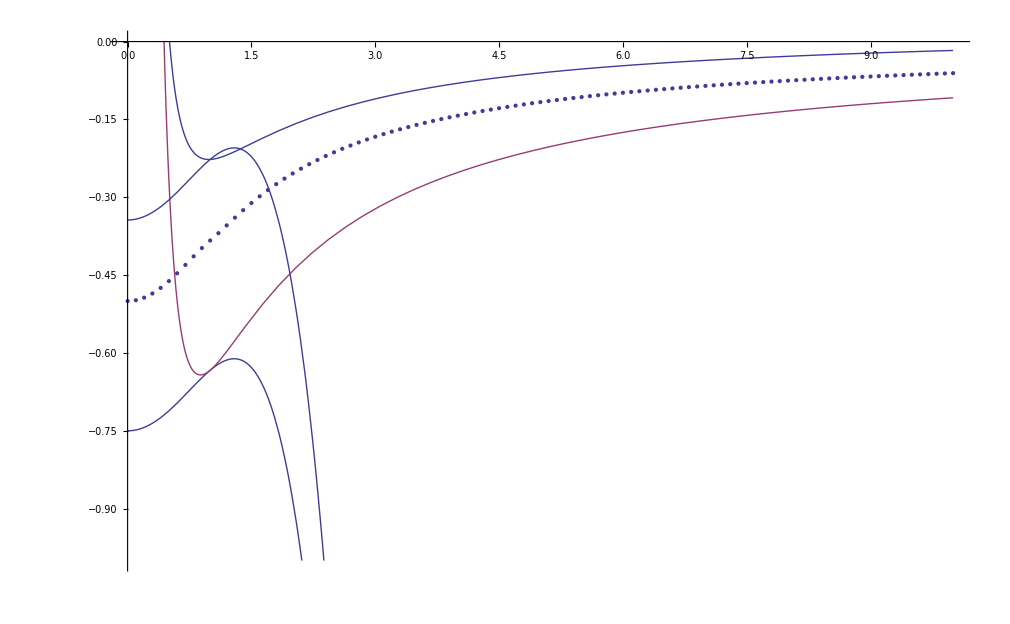

```mathematica
Show[plot1, plot2, plot3, plot4]
```

```mathematica
contm={{1, -1},{0, 1}};
contv={-1/48, -31/120};
```

```mathematica
homocoeff=LinearSolve[contm, contv]
```

{-67/240,-31/120}

```mathematica
N[homocoeff]
```

{-0.279167,-0.258333}